To fulfil Wolfram Mathematica language requirement, we consider for the following notebook that N = m (no capital letter as a variable).
 We set the integral ∫_r_1^r_2 P( B̄ |U(n),V(n,d)) ρ_n(d) dd  as IntFun, following:

```mathematica
IntFun[r1_?Positive,m_Integer,n_Integer]/;(n>=0&&m>=n+1):=- (m-n) NIntegrate[(1-((4*(d^2)* ArcCos[r1/d]-4 * r1 * Sqrt[d^2-r1^2])/((2*Pi-4)*( r1^2))))^(n)*(1/(r1 *Sqrt[1-(r1^2)/(d^2)])+(2*d* ArcCos[r1/d])/(r1^2)-((4* d* r1)/Sqrt[d^2-r1^2]+2 *d*Pi)/(4*(r1^2)))*(1+(d/r1)^2*ArcCos[r1/d]-((d^2)* Pi+4 *r1* Sqrt[d^2-r1^2])/(4* (r1^2)))^(m-n-1),{d,r1,Sqrt[2]*r1},Method->"GlobalAdaptive",WorkingPrecision->30]
```

We set  P(B̄|U(n) as probaBUm, following:

```mathematica
probaBUm[r1_?Positive,m_Integer,n_Integer]/;(n>=0&&m>=n+1):= (1 -(1-(Pi/4))^(m-n))+IntFun[r1,m,n]
```

We set  P(U(n)) as probaUm, following:

```mathematica
probaUm[m_Integer,n_Integer]/;(n>=0&&m>=n+1):=Binomial[m,n]*(1-(2/Pi))^n*(2/Pi)^(m-n)
```

We set P(A) as complementaryEventProba, following:

```mathematica
probaAm[m_Integer]/;(m>=1):= 1-(1- (2 /Pi))^m
```

We set P(B̄|A) as complementaryEventProba, following:

```mathematica
complementaryEventProba[r1_?Positive,m_Integer]/;(m>=1):=(1 / probaAm[m])*(probaUm[m,0]+ Sum[probaBUm[r1,m,n]*probaUm[m,n],{n,1,m-1}])
```

We set the final probability of error as probaError :

```mathematica
probaError[r1_?Positive,m_Integer]/;(m>=1):=1 - complementaryEventProba[r1,m]
```

Plot the numeric resolution in 2D

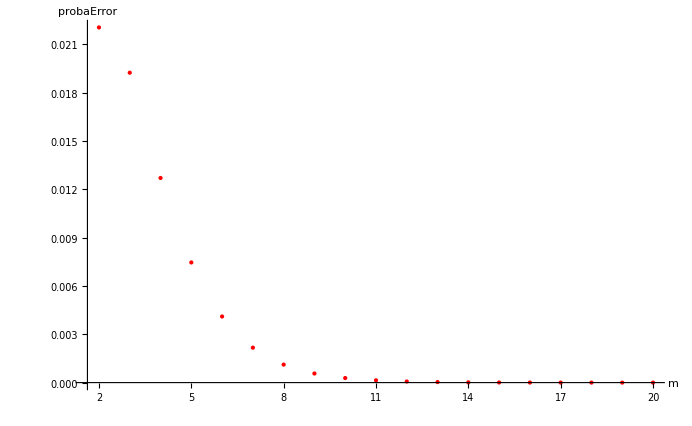

```mathematica
data2D=Table[{m,probaError[50,m]},{m,2,20, 1}];

ListPlot[data2D,PlotRange->All,AxesLabel->{"m","probaError"},PlotStyle->{Red,PointSize[Large]},Ticks->{Table[{m,m},{m,2,20}],Automatic }, LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

Create the data table to plot the Error in 3D to check the value at m = 0 and  verify that probability should be not depending on “a” -search square side length:

```mathematica
mMin=0;
mMax=11;
mStep=1;
r1Min=10;
r1Max=100;
r1Step=5;

data3D=Table[{r1,m,probaError[r1,m]},{m,mMin,mMax, mStep},{r1,r1Min,r1Max,r1Step}];
```

We Flatten the data in one vector:

```mathematica
points3D=Flatten[data3D,1];
```

Plot in 3D:

```mathematica
ListPlot3D[points3D,PlotRange->All,AxesLabel->{"search squarre half side (pix)","cell number","probaError"},InterpolationOrder->0,(*or 1,or 0,depending on how "smooth" you want it*)Mesh->None,Ticks->{Automatic,Table[{i,i},{i,1,10}],Automatic }]
```

-Graphics3D-

Now user can enter the value for a  m they want:

```mathematica
m = 10;
```

```mathematica
probaError[100,m]
```

0.0002827883231769558157209243268